```mathematica
max = 100;
n = 10;
c = 1;
m = 1;
agents = RandomReal[max, {n,2}];
```

```mathematica
ex = Solve[c / 2^exp== 0.1, exp]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{exp→3.32193}}

```mathematica
force= Sum[c / Norm[(agents[[1]] - agents[[i]])]^exp/.ex,{i,2, n}]
```

{0.000034564}

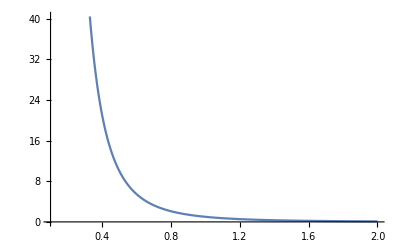

```mathematica
p1 = Plot[c / x^exp/. ex, {x, 0.1, 2}]
```